# < Essay Title (The first cell that is formatted as “Title” will be the title we use for your essay) >

< First and Last name>

Origin of Eigenvalues

Discovered in Cauchy Celestial Mechanics, applied to Newtonian Physics (Oscillations)

Outline

Origin of Eigenvalue

What exactly does it describe?

Real-life applications

The word eigenvalue is German in origin, invented by German mathematician David Hilbert. In his paper titled

```mathematica
TextTranslation["Grundzüge einer allgemeinen Theorie der linearen Integralgleichungen"]
```

Main features of a general theory of linear integral equations

in which he was, as the title suggests, attempting to provide a general theory for a system of linear equations. This is not to suggest that eigenvalues were unused before Hilbert; Euler, LaGrange, Cauchy, Fourier, and many others were all

```mathematica
WordTranslation["eigen","German"->"English"]
```

{own,very own}

#### Definition of the Eigenvalue

Suppose A is an n x n matrix like so

```mathematica
(*Example Code*)
```

```mathematica
Clear[ex]
ex={{0,1,0},{0,0,1},{1,0,0}}
```

{{0,1,0},{0,0,1},{1,0,0}}

```mathematica
MatrixForm[ex]
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)



```mathematica
AdjacencyGraph[ex]
```

```mathematica
Clear[X,x,y,t]
```

```mathematica
c = {{1,1}, {-2,-1}}
```

```mathematica
MatrixForm[c]
```

(1 | 1
-2 | -1)

```mathematica
Eigenvalues[c]
```

{ⅈ,-ⅈ}

```mathematica
X[t_] = {x[t],y[t]};
```

```mathematica
system = X'[t] == c.X[t]
```

{x'[t],y'[t]}=={x[t]+y[t],-2 x[t]-y[t]}

```mathematica
(*Above defines system of equations*)
```

```mathematica
sol = DSolve[system, {x,y},t]
```

{{x→Function[{t},C[2] Sin[t]+C[1] (Cos[t]+Sin[t])],y→Function[{t},C[2] (Cos[t]-Sin[t])-2 C[1] Sin[t]]}}

```mathematica
particularsols=Partition[Flatten[Table[{x[t],y[t]}/.sol/.{C[1]->1/i,C[2]->1/j},{i,-20,20,6},{j,-20,20,6}]],2];
```

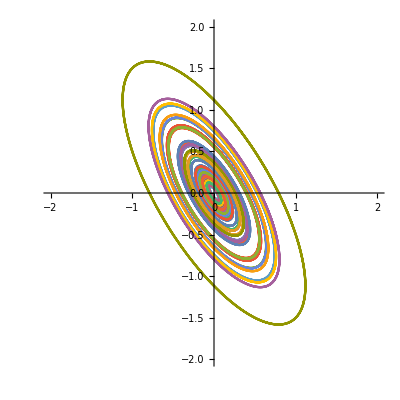

```mathematica
ParametricPlot[Evaluate[particularsols],{t,-10,10}, PlotRange->{-2,2}]
```